```mathematica
Remove["Global`*"];
$Assumptions = k ∈ Reals && Subscript[Σ, d] ∈ Reals && Subscript[Σ, g] ∈ Reals && G ∈ Reals && B ∈ Reals && ϵ ∈ Reals && Subscript[t, s]∈ Reals && Ω∈ Reals && Subscript[c, g]>0 && Subscript[c, d]∈ Reals && Q >0 && λ >0;
A = {{-ⅈ ω , ⅈ Subscript[Σ, g] k, 0 , 0 , 0 , 0},{-ⅈ k((2π G)/Abs[k]-Subscript[c, g]^2/Subscript[Σ, g]), ϵ/Subscript[t, s]-ⅈ ω, -2 Ω, -ⅈ k(2π G)/Abs[k], - ϵ/Subscript[t, s],0},{0, -2B, ϵ/Subscript[t, s]-ⅈ ω,0,0,- ϵ/Subscript[t, s]},{0,0,0,-ⅈ ω,ⅈ Subscript[Σ, d] k,0},{-ⅈ k(2π G)/Abs[k],-1/Subscript[t, s],0,-ⅈ k((2π G)/Abs[k]-Subscript[c, d]^2/Subscript[Σ, d]),1/Subscript[t, s]-ⅈ ω, -2Ω},{0,0,-1/Subscript[t, s],0,-2 B,1/Subscript[t, s]-ⅈ ω}};
H = A+ⅈ ω IdentityMatrix[6];
Print["-------------------------------------------"]
Print["Operator of self-gravitating dusty disk:"]
Print["H=",H//MatrixForm]

U = DiagonalMatrix[{1,-1,-1,1,-1,-1}];
Print["PT symmetry ?"]
Print[":",(U.H.Inverse[U] - Conjugate[H]==0)//Simplify]
```

Remove::rmnsm: There are no symbols matching "Global`*".

-------------------------------------------

Operator of self-gravitating dusty disk:

H=(0 | ⅈ k Σ_g | 0 | 0 | 0 | 0
-ⅈ k ((2 G π)/Abs[k]-c_g^2/Σ_g) | ϵ/t_s | -2 Ω | -(2 ⅈ G k π)/Abs[k] | -ϵ/t_s | 0
0 | -2 B | ϵ/t_s | 0 | 0 | -ϵ/t_s
0 | 0 | 0 | 0 | ⅈ k Σ_d | 0
-(2 ⅈ G k π)/Abs[k] | -1/t_s | 0 | -ⅈ k ((2 G π)/Abs[k]-c_d^2/Σ_d) | 1/t_s | -2 Ω
0 | 0 | -1/t_s | 0 | -2 B | 1/t_s)

PT symmetry ?

:True

```mathematica
(*Change of notation, of variables, and adimensionalization*)
B = -κ^2/4/Ω;
Subscript[Σ, d] = ϵ Subscript[Σ, g];
Subscript[c, d] = Sqrt[ξ] Subscript[c, g];
G = Subscript[c, g] κ / (π Subscript[Σ, g] Q);
Subscript[t, s] = St /κ ;
k = κ/(2 Subscript[c, g] λ)*Q;
κ = 1;
P = DiagonalMatrix[{Subscript[c, g]/Subscript[Σ, g],1,Ω,Subscript[c, g]/Subscript[Σ, g],1,Ω}];
(H2 = (P.H.Inverse[P]//Simplify))//MatrixForm

P2[x_]:=(CharacteristicPolynomial[H2,x]/x//Simplify)
```

(0 | (ⅈ Q)/(2 λ) | 0 | 0 | 0 | 0
(ⅈ (-4+Q^2/λ))/(2 Q) | ϵ/St | -2 | -(2 ⅈ)/Q | -ϵ/St | 0
0 | 1/2 | ϵ/St | 0 | 0 | -ϵ/St
0 | 0 | 0 | 0 | (ⅈ Q ϵ)/(2 λ) | 0
-(2 ⅈ)/Q | -1/St | 0 | -(2 ⅈ)/Q+(ⅈ Q ξ)/(2 ϵ λ) | 1/St | -2
0 | 0 | -1/St | 0 | 1/2 | 1/St)

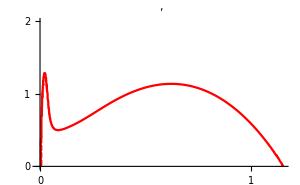

```mathematica
R = (Resultant[P2[x],P2'[x],x]/.St->1/.Q->q^0.5/.ϵ->0.15/.ξ->0.005//Simplify);
p1 = ContourPlot[R==0,{λ,0,1.3},{q,0,5},PlotPoints->50,ContourStyle->Red];
p2 = Plot[-1,{λ,0,3}]; (*trick for Show function*)
Show[p2,p1,Graphics[{Text[Style["",FontSize->12,FontFamily->"Times",Red],{1,1.1},Background->Lighter[Gray, 1]]}],Ticks->{{0,1},{0,1,2}},PlotRange->{{-0.01,1.15},{0,2}},PlotLabel->Style[",  ",Black],AxesLabel->{Style["",Italic,FontSize->12,FontFamily->"Times",Black],Style["",Italic,FontSize->12,FontFamily->"Times",Black]},ImageSize->300]
```

```mathematica
Export["C:\\Users\\Armand\\Documents\\A_travail\\A_these\\symsInAstro\\self_gravity\\marginalStab_dustyToomre.pdf",%]
```

C:\Users\Armand\Documents\A_travail\A_these\symsInAstro\self_gravity\marginalStab_dustyToomre.pdf